## Stability diagram plot

```mathematica
ClearAll["Global`*"];
```

### Defenitions

```mathematica
Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ω=Sqrt[Qp/Qm] ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ]);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
(*M={{-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-Sqrt[(Qm/Qp)] (γp Cos[2 ψ]-γa Sin[2 ψ]),-γa Cos[2 ψ]-γp Sin[2 ψ],γp Cos[2 ψ]-γa Sin[2 ψ],Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-γp Cos[2 ψ]+γa Sin[2 ψ],-γa Cos[2 ψ]-γp Sin[2 ψ],Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-γa Cos[2 ψ]+γp Sin[2 ψ],γp Cos[2 ψ]+γa Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qp/Qm] (-γp Cos[2 ψ]-γa Sin[2 ψ]),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-γp Cos[2 ψ]-γa Sin[2 ψ],-γa Cos[2 ψ]+γp Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};*)
```

#### For gradient method

```mathematica
avars={a5,a4,a3,a2,a1};
vars={Qp,Qm,ψ};
params={Λ,γp};
charpolycoefs={-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((Sqrt[Qm^3 Qp]-Sqrt[Qm Qp^3]) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) Sqrt[Qm Qp] (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm Sqrt[Qm Qp] α γ γa Sin[4 ψ]+Qp Sqrt[Qm Qp] α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm Sqrt[Qm Qp] γd γp Sin[4 ψ]-Qp Sqrt[Qm Qp] γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+Sqrt[Qm Qp^5]) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((Sqrt[Qm^5 Qp]-3 Sqrt[Qm Qp^5]) γa-(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp Sqrt[Qm Qp] α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm Sqrt[Qm Qp] α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 Sqrt[Qm^3 Qp] γ γa+4 Sqrt[Qm Qp] γa γd+4 Sqrt[Qm^3 Qp] γa γd+4 Sqrt[Qm Qp^3] γa γd-Sqrt[Qm^5 Qp] γa κ+3 Sqrt[Qm Qp^5] γa κ+Sqrt[Qm^5 Qp] α γp κ+Sqrt[Qm Qp^5] α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 Sqrt[Qm Qp^3] γd γp+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((Sqrt[Qm Qp]+2 Sqrt[Qm^3 Qp]+Sqrt[Qm Qp^3]) γ+Sqrt[Qm Qp] γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+Sqrt[Qm Qp^3] γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
charpolycoefs=charpolycoefs[[1;;5]];
stateqns={
κ(Ns+ns - 1)-γa Sqrt[Qm/Qp] Cos[2 ψ]- γp Sqrt[Qm/Qp]Sin[2 ψ], κ  α(Ns+ns - 1)+γa Sqrt[Qm/Qp] Sin[2 ψ]-γp Sqrt[Qm/Qp]Cos[2 ψ]-ω,κ (Ns-ns- 1)-γa Sqrt[Qp/Qm]Cos[2 ψ]+ γp Sqrt[Qp/Qm] Sin[2 ψ],κ  α(Ns-ns - 1)-γa Sqrt[Qp/Qm]Sin[2 ψ]-γp Sqrt[Qp/Qm]Cos[2 ψ]-ω,-γ(Ns -Λ)-γ(Ns+ns) Qp-γ(Ns-ns) Qm,-γd ns-γ(Ns+ns) Qp+γ(Ns-ns) Qm};
stateqns[[2]]=stateqns[[2]]-stateqns[[4]]//FullSimplify;
stateqns=Drop[stateqns,{4}];
HwM={
{a1,a3,a5,0},
{1,a2,a4,0},
{0,a1,a3,a5},
{0,1,a2,a4}};
dDda=Table[D[Det[HwM],avars[[i]]],{i,1,5}];
dadx=Table[D[charpolycoefs[[i]],vars[[j]]],{i,1,5},{j,1,3}];
dadp=Table[D[charpolycoefs[[i]],params[[j]]],{i,1,5},{j,1,2}];
solNn = Solve[stateqns[[4;;5]]==0,vars[[4;;5]]][[1]]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns = stateqns[[1;;3]]/.solNn//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
dfdx=Table[D[stat3eqns[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dfdp=Table[D[stat3eqns[[i]],params[[j]]],{i,1,3},{j,1,2}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
```

### Solution

```mathematica
(*Solving stationary problem*)
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}]
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];


(*Evaluating charpoly*)

p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p=charpolycoefs/.Nsol;
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
If[AllTrue[p,Positive],
If[AllTrue[Dets,Positive],
Print["System is stable"];
Print[p//MatrixForm];
Print[Dets//MatrixForm],
Print["Some Hurwitz determinants are negative:"];
Print[p//MatrixForm];
Print[Dets//MatrixForm]
],
Print["Some p < 0"];
Print[p//MatrixForm]
]
```

{Qp→0.350028,Qm→0.350028,a→-1.0848×10^-16}

System is stable

(1.72189×10^-11
9475.07
3330.64
504.776
104.807)

(49573.6
5.78288×10^11)

```mathematica
p
```

{1.72189×10^-11,9475.07,3330.64,504.776,104.807}

```mathematica
({{3.232764872790355*^-8}, {1.910655999879378*^7}, {422611.74144311715}, {68199.01081752068}, {1328.32937396901}, {52.44011333711123}, {1}})({{52.44011333711123}, {1458.7321024281991}, {-6.073344503642392*^7}, {-4.313731141096*^12}, {-8.24205628660157*^19}}){Qp->0.3500283342778091,Qm->0.35002833427780905,a->-1.0848001355988288*^-16}
```

### Plotting by pixels v0

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;

If[AllTrue[p[[2;;]],Positive],
Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)
(*DH[[1]]=p[[6]];
DH[[2]]=p[[6]]*p[[5]]-p[[7]]*p[[4]];
DH[[3]]=p[[4]]*DH[[2]]-p[[6]]*p[[6]]*p[[3]]+p[[2]]*p[[7]]*p[[6]];DH[[4]]=p[[3]]*DH[[3]]+p[[7]]*p[[2]]*(p[[5]]*p[[4]]-p[[7]]*p[[2]])-p[[6]]*(p[[5]]*p[[5]]*p[[2]]-p[[7]]*p[[3]]*p[[2]]-p[[1]]*DH[[2]]);DH[[5]]=p[[2]]*DH[[4]]+p[[1]]*(p[[7]]*p[[4]]*p[[4]]*p[[4]]-p[[6]]*p[[4]]*(p[[5]]*p[[4]]+2*p[[7]]*p[[2]])+p[[6]]*p[[6]]*(p[[4]]*p[[3]]+p[[5]]*p[[2]])-p[[6]]*p[[6]]*p[[6]]*p[[1]]);*)

If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result[[i,j]]=1,result[[i,j]]=0.7],
result[[i,j]]=0.5;
]
(*result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] ***=> D4 fails****)
,
result[[i,j]]=0;
]
]
];
Image[Reverse[result]]
```

-Graphics-

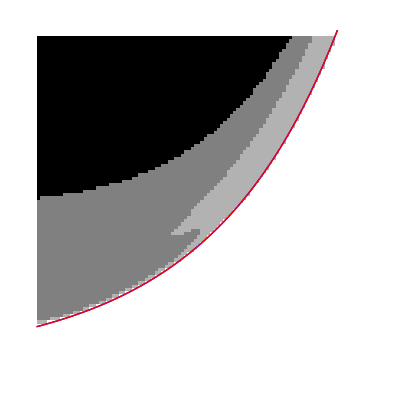

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuMine[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
Diff[γp_]:=(MuMine[γp]-Mu[γp])/MuMine[γp];

lp=Plot[(Mu[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];
lmp=Plot[(MuMine[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick}];
Show[ap,lmp,lp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

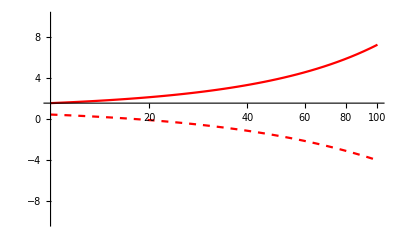

```mathematica
pl1 = Plot[1+γd*x/(γ (α κ - x)),{x,10,100},PlotStyle->Red,ScalingFunctions-> {"Log10",None}];
pl2 =Plot[1-γd/γ+2α x/γ,{x,10,100},PlotStyle->Blue,ScalingFunctions-> {"Log10",None}];
pl3 = Plot[1-γd*x/(γ (α κ + x)),{x,10,100},PlotStyle->{Red,Dashed},ScalingFunctions-> {"Log10",None}];
pl4 =Plot[1-γd/γ-2α x/γ,{x,10,100},PlotStyle->{Blue,Dashed},ScalingFunctions-> {"Log10",None}];
Show[pl1,pl2,pl3,pl4,PlotRange-> {{1,2},{-10,10}}]
```

```mathematica
oldresult=result;
```

### Plotting by pixels v2

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
If[oldresult[[i,j]]>0.5,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];

p=charpolycoefs/.Nsol;

If[AllTrue[p,Positive],
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)

If[AllTrue[Dets,Positive],
result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] 
,
result[[i,j]]=0
]
],Print[i," ",j];]
]];
Image[Reverse[result]]
```

14 1

14 2

14 3

14 4

15 1

15 2

15 3

15 4

15 5

15 6

15 7

15 8

16 1

16 2

16 3

16 4

16 5

16 6

16 7

16 8

16 9

16 10

16 11

17 1

17 2

17 3

17 4

17 5

17 6

17 7

17 8

17 9

17 10

17 11

17 12

17 13

17 14

18 1

18 2

18 3

18 4

18 5

18 6

18 7

18 8

18 9

18 10

18 11

18 12

18 13

18 14

18 15

18 16

19 1

19 2

19 3

19 4

19 5

19 6

19 7

19 8

19 9

19 10

19 11

19 12

19 13

19 14

19 15

19 16

19 17

19 18

19 19

20 1

20 2

20 3

20 4

20 5

20 6

20 7

20 8

20 9

20 10

20 11

20 12

20 13

20 14

20 15

20 16

20 17

20 18

20 19

20 20

20 21

21 1

21 2

21 3

21 4

21 5

21 6

21 7

21 8

21 9

21 10

21 11

21 12

21 13

21 14

21 15

21 16

21 17

21 18

21 19

21 20

21 21

21 22

21 23

22 1

22 2

22 3

22 4

22 5

22 6

22 7

22 8

22 9

22 10

22 11

22 12

22 13

22 14

22 15

22 16

22 17

22 18

22 19

22 20

22 21

22 22

22 23

22 24

22 25

23 1

23 2

23 3

23 4

23 5

23 6

23 7

23 8

23 9

23 10

23 11

23 12

23 13

23 14

23 15

23 16

23 17

23 18

23 19

23 20

23 21

23 22

23 23

23 24

23 25

23 26

23 27

24 1

24 2

24 3

24 4

24 5

24 6

24 7

24 8

24 9

24 10

24 11

24 12

24 13

24 14

24 15

24 16

24 17

24 18

24 19

24 20

24 21

24 22

24 23

24 24

24 25

24 26

24 27

24 28

24 29

25 1

25 2

25 3

25 4

25 5

25 6

25 7

25 8

25 9

25 10

25 11

25 12

25 13

25 14

25 15

25 16

25 17

25 18

25 19

25 20

25 21

25 22

25 23

25 24

25 25

25 26

25 27

25 28

25 29

25 30

25 31

26 1

26 2

26 3

26 4

26 5

26 6

26 7

26 8

26 9

26 10

26 11

26 12

26 13

26 14

26 15

26 16

26 17

26 18

26 19

26 20

26 21

26 22

26 23

26 24

26 25

26 26

26 27

26 28

26 29

26 30

26 31

26 32

26 33

27 1

27 2

27 3

27 4

27 5

27 6

27 7

27 8

27 9

27 10

27 11

27 12

27 13

27 14

27 15

27 16

27 17

27 18

27 19

27 20

27 21

27 22

27 23

27 24

27 25

27 26

27 27

27 28

27 29

27 30

27 31

27 32

27 33

27 34

28 1

28 2

28 3

28 4

28 5

28 6

28 7

28 8

28 9

28 10

28 11

28 12

28 13

28 14

28 15

28 16

28 17

28 18

28 19

28 20

28 21

28 22

28 23

28 24

28 25

28 26

28 27

28 28

28 29

28 30

28 31

28 32

28 33

28 34

28 35

28 36

29 1

29 2

29 3

29 4

29 5

29 6

29 7

29 8

29 9

29 10

29 11

29 12

29 13

29 14

29 15

29 16

29 17

29 18

29 19

29 20

29 21

29 22

29 23

29 24

29 25

29 26

29 27

29 28

29 29

29 30

29 31

29 32

29 33

29 34

29 35

29 36

29 37

30 1

30 2

30 3

30 4

30 5

30 6

30 7

30 8

30 9

30 10

30 11

30 12

30 13

30 14

30 15

30 16

30 17

30 18

30 19

30 20

30 21

30 22

30 23

30 24

30 25

30 26

30 27

30 28

30 29

30 30

30 31

30 32

30 33

30 34

30 35

30 36

30 37

30 38

30 39

31 1

31 2

31 3

31 4

31 5

31 6

31 7

31 8

31 9

31 10

31 11

31 12

31 13

31 14

31 15

31 16

31 17

31 18

31 19

31 20

31 21

31 22

31 23

31 24

31 25

31 26

31 27

31 28

31 29

31 30

31 31

31 32

31 33

31 34

31 35

31 36

31 37

31 38

31 39

31 40

32 1

32 2

32 3

32 4

32 5

32 6

32 7

32 8

32 9

32 10

32 11

32 12

32 13

32 14

32 15

32 16

32 17

32 18

32 19

32 20

32 21

32 22

32 23

32 24

32 25

32 26

32 27

32 28

32 29

32 30

32 31

32 32

32 33

32 34

32 35

32 36

32 37

32 38

32 39

32 40

32 41

32 42

33 1

33 2

33 3

33 4

33 5

33 6

33 7

33 8

33 9

33 10

33 11

33 12

33 13

33 14

33 15

33 16

33 17

33 18

33 19

33 20

33 21

33 22

33 23

33 24

33 25

33 26

33 27

33 28

33 29

33 30

33 31

33 32

33 33

33 34

33 35

33 36

33 37

33 38

33 39

33 40

33 41

33 42

33 43

34 1

34 2

34 3

34 4

34 5

34 6

34 7

34 8

34 9

34 10

34 11

34 12

34 13

34 14

34 15

34 16

34 17

34 18

34 19

34 20

34 21

34 22

34 23

34 24

34 25

34 26

34 27

34 28

34 29

34 30

34 31

34 32

34 33

34 34

34 35

34 36

34 37

34 38

34 39

34 40

34 41

34 42

34 43

34 44

35 1

35 2

35 3

35 4

35 5

35 6

35 7

35 8

35 9

35 10

35 11

35 12

35 13

35 14

35 15

35 16

35 17

35 18

35 19

35 20

35 21

35 22

35 23

35 24

35 25

35 26

35 27

35 28

35 29

35 30

35 31

35 32

35 33

35 34

35 35

35 36

35 37

35 38

35 39

35 40

35 41

35 42

35 43

35 44

35 45

36 1

36 2

36 3

36 4

36 5

36 6

36 7

36 8

36 9

36 10

36 11

36 12

36 13

36 14

36 15

36 16

36 17

36 18

36 19

36 20

36 21

36 22

36 23

36 24

36 25

36 26

36 27

36 28

36 29

36 30

36 31

36 32

36 33

36 34

36 35

36 36

36 37

36 38

36 39

36 40

36 41

36 42

36 43

36 44

36 45

36 46

37 1

37 2

37 3

37 4

37 5

37 6

37 7

37 8

37 9

37 10

37 11

37 12

37 13

37 14

37 15

37 16

37 17

37 18

37 19

37 20

37 21

37 22

37 23

37 24

37 25

37 26

37 27

37 28

37 29

37 30

37 31

37 32

37 33

37 34

37 35

37 36

37 37

37 38

37 39

37 40

37 41

37 42

37 43

37 44

37 45

37 46

37 47

38 1

38 2

38 3

38 4

38 5

38 6

38 7

38 8

38 9

38 10

38 11

38 12

38 13

38 14

38 15

38 16

38 17

38 18

38 19

38 20

38 21

38 22

38 23

38 24

38 25

38 26

38 27

38 28

38 29

38 30

38 31

38 32

38 33

38 34

38 35

38 36

38 37

38 38

38 39

38 40

38 41

38 42

38 43

38 44

38 45

38 46

38 47

38 48

39 1

39 2

39 3

39 4

39 5

39 6

39 7

39 8

39 9

39 10

39 11

39 12

39 13

39 14

39 15

39 16

39 17

39 18

39 19

39 20

39 21

39 22

39 23

39 24

39 25

39 26

39 27

39 28

39 29

39 30

39 31

39 32

39 33

39 34

39 35

39 36

39 37

39 38

39 39

39 40

39 41

39 42

39 43

39 44

39 45

39 46

39 47

39 48

39 49

40 1

40 2

40 3

40 4

40 5

40 6

40 7

40 8

40 9

40 10

40 11

40 12

40 13

40 14

40 15

40 16

40 17

40 18

40 19

40 20

40 21

40 22

40 23

40 24

40 25

40 26

40 27

40 28

40 29

40 30

40 31

40 32

40 33

40 34

40 35

40 36

40 37

40 38

40 39

40 40

40 41

40 46

40 47

40 48

40 49

40 50

41 1

41 2

41 3

41 4

41 5

41 6

41 7

41 8

41 9

41 10

41 11

41 12

41 13

41 14

41 15

41 16

41 17

41 18

41 19

41 20

41 21

41 22

41 23

41 24

41 25

41 26

41 27

41 28

41 29

41 30

41 31

41 32

41 33

41 34

41 35

41 36

41 37

41 38

41 39

41 40

41 41

41 42

41 48

41 49

41 50

42 1

42 2

42 3

42 4

42 5

42 6

42 7

42 8

42 9

42 10

42 11

42 12

42 13

42 14

42 15

42 16

42 17

42 18

42 19

42 20

42 21

42 22

42 23

42 24

42 25

42 26

42 27

42 28

42 29

42 30

42 31

42 32

42 33

42 34

42 35

42 36

42 37

42 38

42 39

42 40

42 41

42 42

42 43

43 1

43 2

43 3

43 4

43 5

43 6

43 7

43 8

43 9

43 10

43 11

43 12

43 13

43 14

43 15

43 16

43 17

43 18

43 19

43 20

43 21

43 22

43 23

43 24

43 25

43 26

43 27

43 28

43 29

43 30

43 31

43 32

43 33

43 34

43 35

43 36

43 37

43 38

43 39

43 40

43 41

43 42

43 43

43 44

44 1

44 2

44 3

44 4

44 5

44 6

44 7

44 8

44 9

44 10

44 11

44 12

44 13

44 14

44 15

44 16

44 17

44 18

44 19

44 20

44 21

44 22

44 23

44 24

44 25

44 26

44 27

44 28

44 29

44 30

44 31

44 32

44 33

44 34

44 35

44 36

44 37

44 38

44 39

44 40

44 41

44 42

44 43

44 44

44 45

45 1

45 2

45 3

45 4

45 5

45 6

45 7

45 8

45 9

45 10

45 11

45 12

45 13

45 14

45 15

45 16

45 17

45 18

45 19

45 20

45 21

45 22

45 23

45 24

45 25

45 26

45 27

45 28

45 29

45 30

45 31

45 32

45 33

45 34

45 35

45 36

45 37

45 38

45 39

45 40

45 41

45 42

45 43

45 44

45 45

45 46

46 1

46 2

46 3

46 4

46 5

46 6

46 7

46 8

46 9

46 10

46 11

46 12

46 13

46 14

46 15

46 16

46 17

46 18

46 19

46 20

46 21

46 22

46 23

46 24

46 25

46 26

46 27

46 28

46 29

46 30

46 31

46 32

46 33

46 34

46 35

46 36

46 37

46 38

46 39

46 40

46 41

46 42

46 43

46 44

46 45

46 46

46 47

47 1

47 2

47 3

47 4

47 5

47 6

47 7

47 8

47 9

47 10

47 11

47 12

47 13

47 14

47 15

47 16

47 17

47 18

47 19

47 20

47 21

47 22

47 23

47 24

47 25

47 26

47 27

47 28

47 29

47 30

47 31

47 32

47 33

47 34

47 35

47 36

47 37

47 38

47 39

47 40

47 41

47 42

47 43

47 44

47 45

47 46

47 47

48 1

48 2

48 3

48 4

48 5

48 6

48 7

48 8

48 9

48 10

48 11

48 12

48 13

48 14

48 15

48 16

48 17

48 18

48 19

48 20

48 21

48 22

48 23

48 24

48 25

48 26

48 27

48 28

48 29

48 30

48 31

48 32

48 33

48 34

48 35

48 36

48 37

48 38

48 39

48 40

48 41

48 42

48 43

48 44

48 45

48 46

48 47

48 48

49 1

49 2

49 3

49 4

49 5

49 6

49 7

49 8

49 9

49 10

49 11

49 12

49 13

49 14

49 15

49 16

49 17

49 18

49 19

49 20

49 21

49 22

49 23

49 24

49 25

49 26

49 27

49 28

49 29

49 30

49 31

49 32

49 33

49 34

49 35

49 36

49 37

49 38

49 39

49 40

49 41

49 42

49 43

49 44

49 45

49 46

49 47

49 48

49 49

50 1

50 2

50 3

50 4

50 5

50 6

50 7

50 8

50 9

50 10

50 11

50 12

50 13

50 14

50 15

50 16

50 17

50 18

50 19

50 20

50 21

50 22

50 23

50 24

50 25

50 26

50 27

50 28

50 29

50 30

50 31

50 32

50 33

50 34

50 35

50 36

50 37

50 38

50 39

50 40

50 41

50 42

50 43

50 44

50 45

50 46

50 47

50 48

50 49

50 50

51 1

51 2

51 3

51 4

51 5

51 6

51 7

51 8

51 9

51 10

51 11

51 12

51 13

51 14

51 15

51 16

51 17

51 18

51 19

51 20

51 21

51 22

51 23

51 24

51 25

51 26

51 27

51 28

51 29

51 30

51 31

51 32

51 33

51 34

51 35

51 36

51 37

51 38

51 39

51 40

51 41

51 42

51 43

51 44

51 45

51 46

51 47

51 48

51 49

51 50

51 51

52 1

52 2

52 3

52 4

52 5

52 6

52 7

52 8

52 9

52 10

52 11

52 12

52 13

52 14

52 15

52 16

52 17

52 18

52 19

52 20

52 21

52 22

52 23

52 24

52 25

52 26

52 27

52 28

52 29

52 30

52 31

52 32

52 33

52 34

52 35

52 36

52 37

52 38

52 39

52 40

52 41

52 42

52 43

52 44

52 45

52 46

52 47

52 48

52 49

52 50

52 51

52 52

53 1

53 2

53 3

53 4

53 5

53 6

53 7

53 8

53 9

53 10

53 11

53 12

53 13

53 14

53 15

53 16

53 17

53 18

53 19

53 20

53 21

53 22

53 23

53 24

53 25

53 26

53 27

53 28

53 29

53 30

53 31

53 32

53 33

53 34

53 35

53 36

53 37

53 38

53 39

53 40

53 41

53 42

53 43

53 44

53 45

53 46

53 47

53 48

53 49

53 50

53 51

53 52

53 53

54 1

54 2

54 3

54 4

54 5

54 6

54 7

54 8

54 9

54 10

54 11

54 12

54 13

54 14

54 15

54 16

54 17

54 18

54 19

54 20

54 21

54 22

54 23

54 24

54 25

54 26

54 27

54 28

54 29

54 30

54 31

54 32

54 33

54 34

54 35

54 36

54 37

54 38

54 39

54 40

54 41

54 42

54 43

54 44

54 45

54 46

54 47

54 48

54 49

54 50

54 51

54 52

54 53

54 54

55 1

55 2

55 3

55 4

55 5

55 6

55 7

55 8

55 9

55 10

55 11

55 12

55 13

55 14

55 15

55 16

55 17

55 18

55 19

55 20

55 21

55 22

55 23

55 24

55 25

55 26

55 27

55 28

55 29

55 30

55 31

55 32

55 33

55 34

55 35

55 36

55 37

55 38

55 39

55 40

55 41

55 42

55 43

55 44

55 45

55 46

55 47

55 48

55 49

55 50

55 51

55 52

55 53

55 54

55 55

56 1

56 2

56 3

56 4

56 5

56 6

56 7

56 8

56 9

56 10

56 11

56 12

56 13

56 14

56 15

56 16

56 17

56 18

56 19

56 20

56 21

56 22

56 23

56 24

56 25

56 26

56 27

56 28

56 29

56 30

56 31

56 32

56 33

56 34

56 35

56 36

56 37

56 38

56 39

56 40

56 41

56 42

56 43

56 44

56 45

56 46

56 47

56 48

56 49

56 50

56 51

56 52

56 53

56 54

56 55

56 56

57 1

57 2

57 3

57 4

57 5

57 6

57 7

57 8

57 9

57 10

57 11

57 12

57 13

57 14

57 15

57 16

57 17

57 18

57 19

57 20

57 21

57 22

57 23

57 24

57 25

57 26

57 27

57 28

57 29

57 30

57 31

57 32

57 33

57 34

57 35

57 36

57 37

57 38

57 39

57 40

57 41

57 42

57 43

57 44

57 45

57 46

57 47

57 48

57 49

57 50

57 51

57 52

57 53

57 54

57 55

57 56

57 57

58 1

58 2

58 3

58 4

58 5

58 6

58 7

58 8

58 9

58 10

58 11

58 12

58 13

58 14

58 15

58 16

58 17

58 18

58 19

58 20

58 21

58 22

58 23

58 24

58 25

58 26

58 27

58 28

58 29

58 30

58 31

58 32

58 33

58 34

58 35

58 36

58 37

58 38

58 39

58 40

58 41

58 42

58 43

58 44

58 45

58 46

58 47

58 48

58 49

58 50

58 51

58 52

58 53

58 54

58 55

58 56

58 57

58 58

59 1

59 2

59 3

59 4

59 5

59 6

59 7

59 8

59 9

59 10

59 11

59 12

59 13

59 14

59 15

59 16

59 17

59 18

59 19

59 20

59 21

59 22

59 23

59 24

59 25

59 26

59 27

59 28

59 29

59 30

59 31

59 32

59 33

59 34

59 35

59 36

59 37

59 38

59 39

59 40

59 41

59 42

59 43

59 44

59 45

59 46

59 47

59 48

59 49

59 50

59 51

59 52

59 53

59 54

59 55

59 56

59 57

59 58

60 1

60 2

60 3

60 4

60 5

60 6

60 7

60 8

60 9

60 10

60 11

60 12

60 13

60 14

60 15

60 16

60 17

60 18

60 19

60 20

60 21

60 22

60 23

60 24

60 25

60 26

60 27

60 28

60 29

60 30

60 31

60 32

60 33

60 34

60 35

60 36

60 37

60 38

60 39

60 40

60 41

60 42

60 43

60 44

60 45

60 46

60 47

60 48

60 49

60 50

60 51

60 52

60 53

60 54

60 55

60 56

60 57

60 58

60 59

61 1

61 2

61 3

61 4

61 5

61 6

61 7

61 8

61 9

61 10

61 11

61 12

61 13

61 14

61 15

61 16

61 17

61 18

61 19

61 20

61 21

61 22

61 23

61 24

61 25

61 26

61 27

61 28

61 29

61 30

61 31

61 32

61 33

61 34

61 35

61 36

61 37

61 38

61 39

61 40

61 41

61 42

61 43

61 44

61 45

61 46

61 47

61 48

61 49

61 50

61 51

61 52

61 53

61 54

61 55

61 56

61 57

61 58

61 59

61 60

62 1

62 2

62 3

62 4

62 5

62 6

62 7

62 8

62 9

62 10

62 11

62 12

62 13

62 14

62 15

62 16

62 17

62 18

62 19

62 20

62 21

62 22

62 23

62 24

62 25

62 26

62 27

62 28

62 29

62 30

62 31

62 32

62 33

62 34

62 35

62 36

62 37

62 38

62 39

62 40

62 41

62 42

62 43

62 44

62 45

62 46

62 47

62 48

62 49

62 50

62 51

62 52

62 53

62 54

62 55

62 56

62 57

62 58

62 59

62 60

62 61

63 1

63 2

63 3

63 4

63 5

63 6

63 7

63 8

63 9

63 10

63 11

63 12

63 13

63 14

63 15

63 16

63 17

63 18

63 19

63 20

63 21

63 22

63 23

63 24

63 25

63 26

63 27

63 28

63 29

63 30

63 31

63 32

63 33

63 34

63 35

63 36

63 37

63 38

63 39

63 40

63 41

63 42

63 43

63 44

63 45

63 46

63 47

63 48

63 49

63 50

63 51

63 52

63 53

63 54

63 55

63 56

63 57

63 58

63 59

63 60

63 61

63 62

64 1

64 2

64 3

64 4

64 5

64 6

64 7

64 8

64 9

64 10

64 11

64 12

64 13

64 14

64 15

64 16

64 17

64 18

64 19

64 20

64 21

64 22

64 23

64 24

64 25

64 26

64 27

64 28

64 29

64 30

64 31

64 32

64 33

64 34

64 35

64 36

64 37

64 38

64 39

64 40

64 41

64 42

64 43

64 44

64 45

64 46

64 47

64 48

64 49

64 50

64 51

64 52

64 53

64 54

64 55

64 56

64 57

64 58

64 59

64 60

64 61

64 62

65 1

65 2

65 3

65 4

65 5

65 6

65 7

65 8

65 9

65 10

65 11

65 12

65 13

65 14

65 15

65 16

65 17

65 18

65 19

65 20

65 21

65 22

65 23

65 24

65 25

65 26

65 27

65 28

65 29

65 30

65 31

65 32

65 33

65 34

65 35

65 36

65 37

65 38

65 39

65 40

65 41

65 42

65 43

65 44

65 45

65 46

65 47

65 48

65 49

65 50

65 51

65 52

65 53

65 54

65 55

65 56

65 57

65 58

65 59

65 60

65 61

65 62

65 63

66 1

66 2

66 3

66 4

66 5

66 6

66 7

66 8

66 9

66 10

66 11

66 12

66 13

66 14

66 15

66 16

66 17

66 18

66 19

66 20

66 21

66 22

66 23

66 24

66 25

66 26

66 27

66 28

66 29

66 30

66 31

66 32

66 33

66 34

66 35

66 36

66 37

66 38

66 39

66 40

66 41

66 42

66 43

66 44

66 45

66 46

66 47

66 48

66 49

66 50

66 51

66 52

66 53

66 54

66 55

66 56

66 57

66 58

66 59

66 60

66 61

66 62

66 63

66 64

67 1

67 2

67 3

67 4

67 5

67 6

67 7

67 8

67 9

67 10

67 11

67 12

67 13

67 14

67 15

67 16

67 17

67 18

67 19

67 20

67 21

67 22

67 23

67 24

67 25

67 26

67 27

67 28

67 29

67 30

67 31

67 32

67 33

67 34

67 35

67 36

67 37

67 38

67 39

67 40

67 41

67 42

67 43

67 44

67 45

67 46

67 47

67 48

67 49

67 50

67 51

67 52

67 53

67 54

67 55

67 56

67 57

67 58

67 59

67 60

67 61

67 62

67 63

67 64

67 65

68 1

68 2

68 3

68 4

68 5

68 6

68 7

68 8

68 9

68 10

68 11

68 12

68 13

68 14

68 15

68 16

68 17

68 18

68 19

68 20

68 21

68 22

68 23

68 24

68 25

68 26

68 27

68 28

68 29

68 30

68 31

68 32

68 33

68 34

68 35

68 36

68 37

68 38

68 39

68 40

68 41

68 42

68 43

68 44

68 45

68 46

68 47

68 48

68 49

68 50

68 51

68 52

68 53

68 54

68 55

68 56

68 57

68 58

68 59

68 60

68 61

68 62

68 63

68 64

68 65

69 1

69 2

69 3

69 4

69 5

69 6

69 7

69 8

69 9

69 10

69 11

69 12

69 13

69 14

69 15

69 16

69 17

69 18

69 19

69 20

69 21

69 22

69 23

69 24

69 25

69 26

69 27

69 28

69 29

69 30

69 31

69 32

69 33

69 34

69 35

69 36

69 37

69 38

69 39

69 40

69 41

69 42

69 43

69 44

69 45

69 46

69 47

69 48

69 49

69 50

69 51

69 52

69 53

69 54

69 55

69 56

69 57

69 58

69 59

69 60

69 61

69 62

69 63

69 64

69 65

69 66

70 1

70 2

70 3

70 4

70 5

70 6

70 7

70 8

70 9

70 10

70 11

70 12

70 13

70 14

70 15

70 16

70 17

70 18

70 19

70 20

70 21

70 22

70 23

70 24

70 25

70 26

70 27

70 28

70 29

70 30

70 31

70 32

70 33

70 34

70 35

70 36

70 37

70 38

70 39

70 40

70 41

70 42

70 43

70 44

70 45

70 46

70 47

70 48

70 49

70 50

70 51

70 52

70 53

70 54

70 55

70 56

70 57

70 58

70 59

70 60

70 61

70 62

70 63

70 64

70 65

70 66

70 67

71 1

71 2

71 3

71 4

71 5

71 6

71 7

71 8

71 9

71 10

71 11

71 12

71 13

71 14

71 15

71 16

71 17

71 18

71 19

71 20

71 21

71 22

71 23

71 24

71 25

71 26

71 27

71 28

71 29

71 30

71 31

71 32

71 33

71 34

71 35

71 36

71 37

71 38

71 39

71 40

71 41

71 42

71 43

71 44

71 45

71 46

71 47

71 48

71 49

71 50

71 51

71 52

71 53

71 54

71 55

71 56

71 57

71 58

71 59

71 60

71 61

71 62

71 63

71 64

71 65

71 66

71 67

71 68

72 1

72 2

72 3

72 4

72 5

72 6

72 7

72 8

72 9

72 10

72 11

72 12

72 13

72 14

72 15

72 16

72 17

72 18

72 19

72 20

72 21

72 22

72 23

72 24

72 25

72 26

72 27

72 28

72 29

72 30

72 31

72 32

72 33

72 34

72 35

72 36

72 37

72 38

72 39

72 40

72 41

72 42

72 43

72 44

72 45

72 46

72 47

72 48

72 49

72 50

72 51

72 52

72 53

72 54

72 55

72 56

72 57

72 58

72 59

72 60

72 61

72 62

72 63

72 64

72 65

72 66

72 67

72 68

73 1

73 2

73 3

73 4

73 5

73 6

73 7

73 8

73 9

73 10

73 11

73 12

73 13

73 14

73 15

73 16

73 17

73 18

73 19

73 20

73 21

73 22

73 23

73 24

73 25

73 26

73 27

73 28

73 29

73 30

73 31

73 32

73 33

73 34

73 35

73 36

73 37

73 38

73 39

73 40

73 41

73 42

73 43

73 44

73 45

73 46

73 47

73 48

73 49

73 50

73 51

73 52

73 53

73 54

73 55

73 56

73 57

73 58

73 59

73 60

73 61

73 62

73 63

73 64

73 65

73 66

73 67

73 68

73 69

74 1

74 2

74 3

74 4

74 5

74 6

74 7

74 8

74 9

74 10

74 11

74 12

74 13

74 14

74 15

74 16

74 17

74 18

74 19

74 20

74 21

74 22

74 23

74 24

74 25

74 26

74 27

74 28

74 29

74 30

74 31

74 32

74 33

74 34

74 35

74 36

74 37

74 38

74 39

74 40

74 41

74 42

74 43

74 44

74 45

74 46

74 47

74 48

74 49

74 50

74 51

74 52

74 53

74 54

74 55

74 56

74 57

74 58

74 59

74 60

74 61

74 62

74 63

74 64

74 65

74 66

74 67

74 68

74 69

74 70

75 1

75 2

75 3

75 4

75 5

75 6

75 7

75 8

75 9

75 10

75 11

75 12

75 13

75 14

75 15

75 16

75 17

75 18

75 19

75 20

75 21

75 22

75 23

75 24

75 25

75 26

75 27

75 28

75 29

75 30

75 31

75 32

75 33

75 34

75 35

75 36

75 37

75 38

75 39

75 40

75 41

75 42

75 43

75 44

75 45

75 46

75 47

75 48

75 49

75 50

75 51

75 52

75 53

75 54

75 55

75 56

75 57

75 58

75 59

75 60

75 61

75 62

75 63

75 64

75 65

75 66

75 67

75 68

75 69

75 70

76 1

76 2

76 3

76 4

76 5

76 6

76 7

76 8

76 9

76 10

76 11

76 12

76 13

76 14

76 15

76 16

76 17

76 18

76 19

76 20

76 21

76 22

76 23

76 24

76 25

76 26

76 27

76 28

76 29

76 30

76 31

76 32

76 33

76 34

76 35

76 36

76 37

76 38

76 39

76 40

76 41

76 42

76 43

76 44

76 45

76 46

76 47

76 48

76 49

76 50

76 51

76 52

76 53

76 54

76 55

76 56

76 57

76 58

76 59

76 60

76 61

76 62

76 63

76 64

76 65

76 66

76 67

76 68

76 69

76 70

76 71

77 1

77 2

77 3

77 4

77 5

77 6

77 7

77 8

77 9

77 10

77 11

77 12

77 13

77 14

77 15

77 16

77 17

77 18

77 19

77 20

77 21

77 22

77 23

77 24

77 25

77 26

77 27

77 28

77 29

77 30

77 31

77 32

77 33

77 34

77 35

77 36

77 37

77 38

77 39

77 40

77 41

77 42

77 43

77 44

77 45

77 46

77 47

77 48

77 49

77 50

77 51

77 52

77 53

77 54

77 55

77 56

77 57

77 58

77 59

77 60

77 61

77 62

77 63

77 64

77 65

77 66

77 67

77 68

77 69

77 70

77 71

77 72

78 1

78 2

78 3

78 4

78 5

78 6

78 7

78 8

78 9

78 10

78 11

78 12

78 13

78 14

78 15

78 16

78 17

78 18

78 19

78 20

78 21

78 22

78 23

78 24

78 25

78 26

78 27

78 28

78 29

78 30

78 31

78 32

78 33

78 34

78 35

78 36

78 37

78 38

78 39

78 40

78 41

78 42

78 43

78 44

78 45

78 46

78 47

78 48

78 49

78 50

78 51

78 52

78 53

78 54

78 55

78 56

78 57

78 58

78 59

78 60

78 61

78 62

78 63

78 64

78 65

78 66

78 67

78 68

78 69

78 70

78 71

78 72

79 1

79 2

79 3

79 4

79 5

79 6

79 7

79 8

79 9

79 10

79 11

79 12

79 13

79 14

79 15

79 16

79 17

79 18

79 19

79 20

79 21

79 22

79 23

79 24

79 25

79 26

79 27

79 28

79 29

79 30

79 31

79 32

79 33

79 34

79 35

79 36

79 37

79 38

79 39

79 40

79 41

79 42

79 43

79 44

79 45

79 46

79 47

79 48

79 49

79 50

79 51

79 52

79 53

79 54

79 55

79 56

79 57

79 58

79 59

79 60

79 61

79 62

79 63

79 64

79 65

79 66

79 67

79 68

79 69

79 70

79 71

79 72

79 73

80 1

80 2

80 3

80 4

80 5

80 6

80 7

80 8

80 9

80 10

80 11

80 12

80 13

80 14

80 15

80 16

80 17

80 18

80 19

80 20

80 21

80 22

80 23

80 24

80 25

80 26

80 27

80 28

80 29

80 30

80 31

80 32

80 33

80 34

80 35

80 36

80 37

80 38

80 39

80 40

80 41

80 42

80 43

80 44

80 45

80 46

80 47

80 48

80 49

80 50

80 51

80 52

80 53

80 54

80 55

80 56

80 57

80 58

80 59

80 60

80 61

80 62

80 63

80 64

80 65

80 66

80 67

80 68

80 69

80 70

80 71

80 72

80 73

81 1

81 2

81 3

81 4

81 5

81 6

81 7

81 8

81 9

81 10

81 11

81 12

81 13

81 14

81 15

81 16

81 17

81 18

81 19

81 20

81 21

81 22

81 23

81 24

81 25

81 26

81 27

81 28

81 29

81 30

81 31

81 32

81 33

81 34

81 35

81 36

81 37

81 38

81 39

81 40

81 41

81 42

81 43

81 44

81 45

81 46

81 47

81 48

81 49

81 50

81 51

81 52

81 53

81 54

81 55

81 56

81 57

81 58

81 59

81 60

81 61

81 62

81 63

81 64

81 65

81 66

81 67

81 68

81 69

81 70

81 71

81 72

81 73

81 74

82 1

82 2

82 3

82 4

82 5

82 6

82 7

82 8

82 9

82 10

82 11

82 12

82 13

82 14

82 15

82 16

82 17

82 18

82 19

82 20

82 21

82 22

82 23

82 24

82 25

82 26

82 27

82 28

82 29

82 30

82 31

82 32

82 33

82 34

82 35

82 36

82 37

82 38

82 39

82 40

82 41

82 42

82 43

82 44

82 45

82 46

82 47

82 48

82 49

82 50

82 51

82 52

82 53

82 54

82 55

82 56

82 57

82 58

82 59

82 60

82 61

82 62

82 63

82 64

82 65

82 66

82 67

82 68

82 69

82 70

82 71

82 72

82 73

82 74

82 75

83 1

83 2

83 3

83 4

83 5

83 6

83 7

83 8

83 9

83 10

83 11

83 12

83 13

83 14

83 15

83 16

83 17

83 18

83 19

83 20

83 21

83 22

83 23

83 24

83 25

83 26

83 27

83 28

83 29

83 30

83 31

83 32

83 33

83 34

83 35

83 36

83 37

83 38

83 39

83 40

83 41

83 42

83 43

83 44

83 45

83 46

83 47

83 48

83 49

83 50

83 51

83 52

83 53

83 54

83 55

83 56

83 57

83 58

83 59

83 60

83 61

83 62

83 63

83 64

83 65

83 66

83 67

83 68

83 69

83 70

83 71

83 72

83 73

83 74

83 75

84 1

84 2

84 3

84 4

84 5

84 6

84 7

84 8

84 9

84 10

84 11

84 12

84 13

84 14

84 15

84 16

84 17

84 18

84 19

84 20

84 21

84 22

84 23

84 24

84 25

84 26

84 27

84 28

84 29

84 30

84 31

84 32

84 33

84 34

84 35

84 36

84 37

84 38

84 39

84 40

84 41

84 42

84 43

84 44

84 45

84 46

84 47

84 48

84 49

84 50

84 51

84 52

84 53

84 54

84 55

84 56

84 57

84 58

84 59

84 60

84 61

84 62

84 63

84 64

84 65

84 66

84 67

84 68

84 69

84 70

84 71

84 72

84 73

84 74

84 75

84 76

85 1

85 2

85 3

85 4

85 5

85 6

85 7

85 8

85 9

85 10

85 11

85 12

85 13

85 14

85 15

85 16

85 17

85 18

85 19

85 20

85 21

85 22

85 23

85 24

85 25

85 26

85 27

85 28

85 29

85 30

85 31

85 32

85 33

85 34

85 35

85 36

85 37

85 38

85 39

85 40

85 41

85 42

85 43

85 44

85 45

85 46

85 47

85 48

85 49

85 50

85 51

85 52

85 53

85 54

85 55

85 56

85 57

85 58

85 59

85 60

85 61

85 62

85 63

85 64

85 65

85 66

85 67

85 68

85 69

85 70

85 71

85 72

85 73

85 74

85 75

85 76

86 1

86 2

86 3

86 4

86 5

86 6

86 7

86 8

86 9

86 10

86 11

86 12

86 13

86 14

86 15

86 16

86 17

86 18

86 19

86 20

86 21

86 22

86 23

86 24

86 25

86 26

86 27

86 28

86 29

86 30

86 31

86 32

86 33

86 34

86 35

86 36

86 37

86 38

86 39

86 40

86 41

86 42

86 43

86 44

86 45

86 46

86 47

86 48

86 49

86 50

86 51

86 52

86 53

86 54

86 55

86 56

86 57

86 58

86 59

86 60

86 61

86 62

86 63

86 64

86 65

86 66

86 67

86 68

86 69

86 70

86 71

86 72

86 73

86 74

86 75

86 76

86 77

87 1

87 2

87 3

87 4

87 5

87 6

87 7

87 8

87 9

87 10

87 11

87 12

87 13

87 14

87 15

87 16

87 17

87 18

87 19

87 20

87 21

87 22

87 23

87 24

87 25

87 26

87 27

87 28

87 29

87 30

87 31

87 32

87 33

87 34

87 35

87 36

87 37

87 38

87 39

87 40

87 41

87 42

87 43

87 44

87 45

87 46

87 47

87 48

87 49

87 50

87 51

87 52

87 53

87 54

87 55

87 56

87 57

87 58

87 59

87 60

87 61

87 62

87 63

87 64

87 65

87 66

87 67

87 68

87 69

87 70

87 71

87 72

87 73

87 74

87 75

87 76

87 77

88 1

88 2

88 3

88 4

88 5

88 6

88 7

88 8

88 9

88 10

88 11

88 12

88 13

88 14

88 15

88 16

88 17

88 18

88 19

88 20

88 21

88 22

88 23

88 24

88 25

88 26

88 27

88 28

88 29

88 30

88 31

88 32

88 33

88 34

88 35

88 36

88 37

88 38

88 39

88 40

88 41

88 42

88 43

88 44

88 45

88 46

88 47

88 48

88 49

88 50

88 51

88 52

88 53

88 54

88 55

88 56

88 57

88 58

88 59

88 60

88 61

88 62

88 63

88 64

88 65

88 66

88 67

88 68

88 69

88 70

88 71

88 72

88 73

88 74

88 75

88 76

88 77

88 78

89 1

89 2

89 3

89 4

89 5

89 6

89 7

89 8

89 9

89 10

89 11

89 12

89 13

89 14

89 15

89 16

89 17

89 18

89 19

89 20

89 21

89 22

89 23

89 24

89 25

89 26

89 27

89 28

89 29

89 30

89 31

89 32

89 33

89 34

89 35

89 36

89 37

89 38

89 39

89 40

89 41

89 42

89 43

89 44

89 45

89 46

89 47

89 48

89 49

89 50

89 51

89 52

89 53

89 54

89 55

89 56

89 57

89 58

89 59

89 60

89 61

89 62

89 63

89 64

89 65

89 66

89 67

89 68

89 69

89 70

89 71

89 72

89 73

89 74

89 75

89 76

89 77

89 78

89 79

90 1

90 2

90 3

90 4

90 5

90 6

90 7

90 8

90 9

90 10

90 11

90 12

90 13

90 14

90 15

90 16

90 17

90 18

90 19

90 20

90 21

90 22

90 23

90 24

90 25

90 26

90 27

90 28

90 29

90 30

90 31

90 32

90 33

90 34

90 35

90 36

90 37

90 38

90 39

90 40

90 41

90 42

90 43

90 44

90 45

90 46

90 47

90 48

90 49

90 50

90 51

90 52

90 53

90 54

90 55

90 56

90 57

90 58

90 59

90 60

90 61

90 62

90 63

90 64

90 65

90 66

90 67

90 68

90 69

90 70

90 71

90 72

90 73

90 74

90 75

90 76

90 77

90 78

90 79

91 1

91 2

91 3

91 4

91 5

91 6

91 7

91 8

91 9

91 10

91 11

91 12

91 13

91 14

91 15

91 16

91 17

91 18

91 19

91 20

91 21

91 22

91 23

91 24

91 25

91 26

91 27

91 28

91 29

91 30

91 31

91 32

91 33

91 34

91 35

91 36

91 37

91 38

91 39

91 40

91 41

91 42

91 43

91 44

91 45

91 46

91 47

91 48

91 49

91 50

91 51

91 52

91 53

91 54

91 55

91 56

91 57

91 58

91 59

91 60

91 61

91 62

91 63

91 64

91 65

91 66

91 67

91 68

91 69

91 70

91 71

91 72

91 73

91 74

91 75

91 76

91 77

91 78

91 79

91 80

92 1

92 2

92 3

92 4

92 5

92 6

92 7

92 8

92 9

92 10

92 11

92 12

92 13

92 14

92 15

92 16

92 17

92 18

92 19

92 20

92 21

92 22

92 23

92 24

92 25

92 26

92 27

92 28

92 29

92 30

92 31

92 32

92 33

92 34

92 35

92 36

92 37

92 38

92 39

92 40

92 41

92 42

92 43

92 44

92 45

92 46

92 47

92 48

92 49

92 50

92 51

92 52

92 53

92 54

92 55

92 56

92 57

92 58

92 59

92 60

92 61

92 62

92 63

92 64

92 65

92 66

92 67

92 68

92 69

92 70

92 71

92 72

92 73

92 74

92 75

92 76

92 77

92 78

92 79

92 80

93 1

93 2

93 3

93 4

93 5

93 6

93 7

93 8

93 9

93 10

93 11

93 12

93 13

93 14

93 15

93 16

93 17

93 18

93 19

93 20

93 21

93 22

93 23

93 24

93 25

93 26

93 27

93 28

93 29

93 30

93 31

93 32

93 33

93 34

93 35

93 36

93 37

93 38

93 39

93 40

93 41

93 42

93 43

93 44

93 45

93 46

93 47

93 48

93 49

93 50

93 51

93 52

93 53

93 54

93 55

93 56

93 57

93 58

93 59

93 60

93 61

93 62

93 63

93 64

93 65

93 66

93 67

93 68

93 69

93 70

93 71

93 72

93 73

93 74

93 75

93 76

93 77

93 78

93 79

93 80

93 81

94 1

94 2

94 3

94 4

94 5

94 6

94 7

94 8

94 9

94 10

94 11

94 12

94 13

94 14

94 15

94 16

94 17

94 18

94 19

94 20

94 21

94 22

94 23

94 24

94 25

94 26

94 27

94 28

94 29

94 30

94 31

94 32

94 33

94 34

94 35

94 36

94 37

94 38

94 39

94 40

94 41

94 42

94 43

94 44

94 45

94 46

94 47

94 48

94 49

94 50

94 51

94 52

94 53

94 54

94 55

94 56

94 57

94 58

94 59

94 60

94 61

94 62

94 63

94 64

94 65

94 66

94 67

94 68

94 69

94 70

94 71

94 72

94 73

94 74

94 75

94 76

94 77

94 78

94 79

94 80

94 81

95 1

95 2

95 3

95 4

95 5

95 6

95 7

95 8

95 9

95 10

95 11

95 12

95 13

95 14

95 15

95 16

95 17

95 18

95 19

95 20

95 21

95 22

95 23

95 24

95 25

95 26

95 27

95 28

95 29

95 30

95 31

95 32

95 33

95 34

95 35

95 36

95 37

95 38

95 39

95 40

95 41

95 42

95 43

95 44

95 45

95 46

95 47

95 48

95 49

95 50

95 51

95 52

95 53

95 54

95 55

95 56

95 57

95 58

95 59

95 60

95 61

95 62

95 63

95 64

95 65

95 66

95 67

95 68

95 69

95 70

95 71

95 72

95 73

95 74

95 75

95 76

95 77

95 78

95 79

95 80

95 81

95 82

96 1

96 2

96 3

96 4

96 5

96 6

96 7

96 8

96 9

96 10

96 11

96 12

96 13

96 14

96 15

96 16

96 17

96 18

96 19

96 20

96 21

96 22

96 23

96 24

96 25

96 26

96 27

96 28

96 29

96 30

96 31

96 32

96 33

96 34

96 35

96 36

96 37

96 38

96 39

96 40

96 41

96 42

96 43

96 44

96 45

96 46

96 47

96 48

96 49

96 50

96 51

96 52

96 53

96 54

96 55

96 56

96 57

96 58

96 59

96 60

96 61

96 62

96 63

96 64

96 65

96 66

96 67

96 68

96 69

96 70

96 71

96 72

96 73

96 74

96 75

96 76

96 77

96 78

96 79

96 80

96 81

96 82

97 1

97 2

97 3

97 4

97 5

97 6

97 7

97 8

97 9

97 10

97 11

97 12

97 13

97 14

97 15

97 16

97 17

97 18

97 19

97 20

97 21

97 22

97 23

97 24

97 25

97 26

97 27

97 28

97 29

97 30

97 31

97 32

97 33

97 34

97 35

97 36

97 37

97 38

97 39

97 40

97 41

97 42

97 43

97 44

97 45

97 46

97 47

97 48

97 49

97 50

97 51

97 52

97 53

97 54

97 55

97 56

97 57

97 58

97 59

97 60

97 61

97 62

97 63

97 64

97 65

97 66

97 67

97 68

97 69

97 70

97 71

97 72

97 73

97 74

97 75

97 76

97 77

97 78

97 79

97 80

97 81

97 82

97 83

98 1

98 2

98 3

98 4

98 5

98 6

98 7

98 8

98 9

98 10

98 11

98 12

98 13

98 14

98 15

98 16

98 17

98 18

98 19

98 20

98 21

98 22

98 23

98 24

98 25

98 26

98 27

98 28

98 29

98 30

98 31

98 32

98 33

98 34

98 35

98 36

98 37

98 38

98 39

98 40

98 41

98 42

98 43

98 44

98 45

98 46

98 47

98 48

98 49

98 50

98 51

98 52

98 53

98 54

98 55

98 56

98 57

98 58

98 59

98 60

98 61

98 62

98 63

98 64

98 65

98 66

98 67

98 68

98 69

98 70

98 71

98 72

98 73

98 74

98 75

98 76

98 77

98 78

98 79

98 80

98 81

98 82

98 83

99 1

99 2

99 3

99 4

99 5

99 6

99 7

99 8

99 9

99 10

99 11

99 12

99 13

99 14

99 15

99 16

99 17

99 18

99 19

99 20

99 21

99 22

99 23

99 24

99 25

99 26

99 27

99 28

99 29

99 30

99 31

99 32

99 33

99 34

99 35

99 36

99 37

99 38

99 39

99 40

99 41

99 42

99 43

99 44

99 45

99 46

99 47

99 48

99 49

99 50

99 51

99 52

99 53

99 54

99 55

99 56

99 57

99 58

99 59

99 60

99 61

99 62

99 63

99 64

99 65

99 66

99 67

99 68

99 69

99 70

99 71

99 72

99 73

99 74

99 75

99 76

99 77

99 78

99 79

99 80

99 81

99 82

99 83

99 84

100 1

100 2

100 3

100 4

100 5

100 6

100 7

100 8

100 9

100 10

100 11

100 12

100 13

100 14

100 15

100 16

100 17

100 18

100 19

100 20

100 21

100 22

100 23

100 24

100 25

100 26

100 27

100 28

100 29

100 30

100 31

100 32

100 33

100 34

100 35

100 36

100 37

100 38

100 39

100 40

100 41

100 42

100 43

100 44

100 45

100 46

100 47

100 48

100 49

100 50

100 51

100 52

100 53

100 54

100 55

100 56

100 57

100 58

100 59

100 60

100 61

100 62

100 63

100 64

100 65

100 66

100 67

100 68

100 69

100 70

100 71

100 72

100 73

100 74

100 75

100 76

100 77

100 78

100 79

100 80

100 81

100 82

100 83

100 84

-Graphics-

```mathematica
Image[Reverse[oldresult-result]]
```

-Graphics-

```mathematica
μ=μs[[100]];
γp=γps[[83]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];
p=charpolycoefs/.Nsol;
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
```

```mathematica
p
```

{1.02348×10^10,1.18555×10^8,-1.30236×10^6,35269.8,121.689}